```mathematica
temp={6.12,                               6.37,             6.64,           6.92,                4.30,                   4.35,            4.96,                  5.42,                      5.66,              5.18};
Hmin={203.5186786,159.935636,107.330364,43.129200,    514.212605, 507.353355  ,425.079007, 342.284699,  297.808353 ,383.788121};
Hmax={187.2120524,141.457458,88.832086,32.1824523,  466.137182, 463.836379,380.516494, 305.250748 , 265.183572 ,346.656475};
area={18.59653432,   12.185609,  7.703442,     2.582175,     96.4697, 102.179158,75.1499006, 54.051132 ,   43.288276,     63.481856};
d=1- (Hmax/Hmin);
a=Transpose@{temp,Hmin};
b=Transpose@{temp,d};
```

```mathematica
FindFit[a,{h(1- (x/n)^2 )},{h,n},x]
```

{h→814.702,n→7.10921}

```mathematica
Show[ListPlot[a, PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" T [K]", " Hc [G]"} ],Plot[{h (1-(x/n)^2)}/.{h->814.7015103766832,n->7.109210151670405},{x,4.26,6.92}],PlotRange->{{4.2,7}, {0,520}}]
```

-Graphics-

```mathematica
Export["C:\\Users\\Peggy\\Desktop\\M2.4 Magnetization of a superconductor\\data\\HcT.jpg",%51,"JPEG"]
```

C:\Users\Peggy\Desktop\M2.4 Magnetization of a superconductor\data\HcT.jpg

```mathematica
(*Integrate[Interpolation[a][x],{x,4.26,6.92}]*)

ab=NonlinearModelFit[a, h(1- (x/n)^2 ),{{h,814.7015103766832},{n,7.109210151670405}},x]
```

FittedModel[814.702 (1-0.019786 x^2)]

```mathematica
ab["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
h | 814.702 | 4.40247 | 185.056 | 8.13648×10^-16
n | 7.10921 | 0.012 | 592.434 | 7.3801×10^-20

```mathematica
ab["AdjustedRSquared"]
```

0.999856

```mathematica
temp1={6.12,                       6.37,                     4.30,                   4.35,            4.96,                  5.42,                      5.66,              5.18};
Hmin1={203.5186786,159.935636,514.212605, 507.353355  ,425.079007, 342.284699,  297.808353 ,383.788121};
Hmax1={187.2120524,141.457458,466.137182, 463.836379,380.516494, 305.250748 , 265.183572 ,346.656475};
d1=1- (Hmax1/Hmin1);
b1=Transpose@{temp1,d1};
```

```mathematica
fit1=LinearModelFit[b1,{1},x]
```

FittedModel[0.0992818]

```mathematica
fit1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0992818 | 0.00436983 | 22.7198 | 8.10474×10^-8

```mathematica
fit1["AdjustedRSquared"]
```

0.

```mathematica
temp2={       6.64,           6.92    };
Hmin2={107.330364,43.129200};
Hmax2={88.832086,32.1824523};
d2=1- (Hmax2/Hmin2);
b2=Transpose@{temp2,d2};
fit2=LinearModelFit[b2,{x},x]
```

FittedModel[-1.75951+0.290943 x]

```mathematica
FittedModel[-1.759510074190568+0.2909426275789593 x]
```

```mathematica
Show[ListPlot[b, PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" T [K]", " D"} ],Plot[{0.09928177000423659},{x,4.25,6.4}],Plot[{-1.759510074190568+0.2909426275789593 x},{x,6.5,6.95}],PlotRange->{{4.2,7.1}, {0,0.3}}]
```

-Graphics-

```mathematica
temp3={6.12,                           6.37,             6.64,           6.92,                    4.35,            4.96,                  5.42,                      5.66,              5.18};
Hmin3={203.5186786,159.935636,107.330364,43.129200, 507.353355  ,425.079007, 342.284699,  297.808353 ,383.788121};
Hmax3={187.2120524,141.457458,88.832086,32.1824523, 463.836379,380.516494, 305.250748 , 265.183572 ,346.656475};
area3={18.59653432,   12.185609,  7.703442,     2.582175,    102.179158,75.1499006, 54.051132 ,   43.288276,     63.481856};
data3=Flatten/@Transpose[{Log[Hmin3],Log[area3]}];
data2=Flatten/@Transpose[{Log[Hmin],Log[area]}];
```

```mathematica
fit4=LinearModelFit[data3,{x},x]
```

FittedModel[-5.07564+1.54234 x]

```mathematica
fit4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5.07564 | 0.393292 | -12.9056 | 3.89664×10^-6
x | 1.54234 | 0.0721552 | 21.3754 | 1.23548×10^-7

```mathematica
fit4["AdjustedRSquared"]
```

0.982755

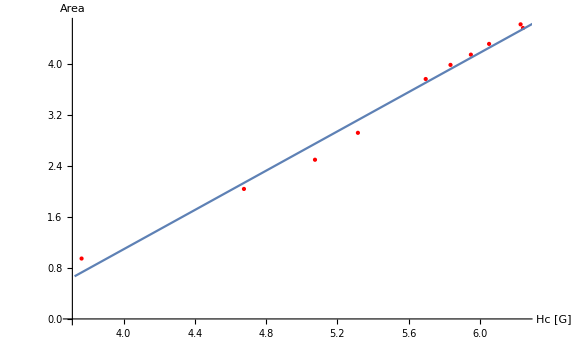

```mathematica
Show[ListPlot[data2, PlotStyle->Directive[Thin,PointSize[Medium],Red,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Hc [G]", " Area"} ],Plot[{-5.075644774593543+1.5423434553742768 x},{x,3.72508,6.5264}]]
```

```mathematica
Export["C:\\Users\\Peggy\\Desktop\\M2.4 Magnetization of a superconductor\\data\\doublog.jpg",%73,"JPEG"]
```

C:\Users\Peggy\Desktop\M2.4 Magnetization of a superconductor\data\doublog.jpg